### Configuration

```mathematica
cfg={pr->2.206*10^7,Dw->0.1,mu->0.005,Kvw->1.2688833653495249*10^-11,qin->-1.,rho->800};
```

### Q space

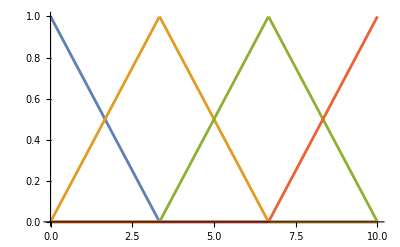

```mathematica
domainsize=10;
nel=3;
xco=Table[(i-1) domainsize/nel,{i,0,nel+2}];
hatfunc[xco_,x_]:=Table[Piecewise[{{0,x<xco[[i]]},{(x-xco[[i]])/(xco[[i+1]]-xco[[i]]),x<xco[[i+1]]},{(xco[[i+2]]-x)/(xco[[i+2]]-xco[[i+1]]),x<xco[[i+2]]}},0],{i,1,Length[xco]-2}]
qphi=hatfunc[xco,x];
dqphi=D[qphi,x];
Plot[{qphi},{x,0,domainsize},PlotRange->All]
```

### P space

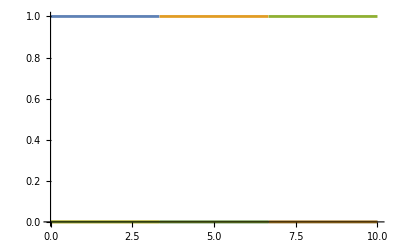

```mathematica
ctefunc[xco_,x_]:=Table[Piecewise[{{0,x<xco[[i]]},{1,x<xco[[i+1]]}},0],{i,1,Length[xco]-2}]
pphi=ctefunc[xco[[2;;-1]],x];
Plot[pphi,{x,0,domainsize},PlotRange->All]
```

### Matrix and vector

```mathematica
ndofsp=Length[pphi];
ndofsq=Length[qphi];
ndofs=ndofsp+ndofsq;
Kg=ConstantArray[0,{ndofs,ndofs}];
Fg=ConstantArray[0,{ndofs}];
Kg[[1;;ndofsq,1;;ndofsq]]=(128 mu)/(Dw^4 π)Table[Integrate[qphi[[i]]qphi[[j]],{x,0,domainsize}],{i,ndofsq},{j,ndofsq}];
Kg[[1;;ndofsq,ndofsq+1;;-1]]=-Table[Integrate[dqphi[[i]]pphi[[j]],{x,0,domainsize}],{i,ndofsq},{j,ndofsp}];
Kg[[ndofsq+1;;,1;;ndofsq]]=Transpose[Kg[[1;;ndofsq,ndofsq+1;;-1]]];
Kg[[ndofsq+1;;,ndofsq+1;;]]=Kvw Table[Integrate[pphi[[i]]pphi[[j]],{x,0,domainsize}],{i,ndofsp},{j,ndofsp}];
Fg[[ndofsq+1;;]]=Kvw pr Table[Integrate[pphi[[i]],{x,0,domainsize}],{i,ndofsp}];
Kg[[ndofsq,;;]]=0;
Kg[[;;,ndofsq]]=0;
Kg[[ndofsq,ndofsq]]=1;
Fg-=qin Kg[[;;,1]];
Kg[[1,;;]]=0;
Kg[[;;,1]]=0;
Kg[[1,1]]=1;
Fg[[1]]=qin;
Fg[[ndofsq]]=0;
Kg=Kg/.cfg;
Fg=Fg/.cfg;
a=LinearSolve[Kg,Fg]//Simplify;
Kg//MatrixForm
Fg//MatrixForm
a
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.,0.,0.,0.,0.,0.,0.},{0.,4527.07,1131.77,0.,-1.,1.,0.},{0.,1131.77,4527.07,0.,0.,-1.,1.},{0.,0.,0.,1.,0.,0.,0.},{0.,-1.,0.,0.,4.22961×10^-11,0.,0.},{0.,1.,-1.,0.,0.,4.22961×10^-11,0.},{0.,0.,1.,0.,0.,0.,4.22961×10^-11}} may contain significant numerical errors.

(1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4527.07 | 1131.77 | 0 | -1 | 1 | 0
0 | 1131.77 | 4527.07 | 0 | 0 | -1 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | -1 | 0 | 0 | 4.22961×10^-11 | 0 | 0
0 | 1 | -1 | 0 | 0 | 4.22961×10^-11 | 0
0 | 0 | 1 | 0 | 0 | 0 | 4.22961×10^-11)

(-1.
1131.77
0
0
1.00093
0.000933052
0.000933052)

{-1.,-0.666667,-0.333333,0.,7.903×10^9,7.90301×10^9,7.90301×10^9}

### Plotting solution

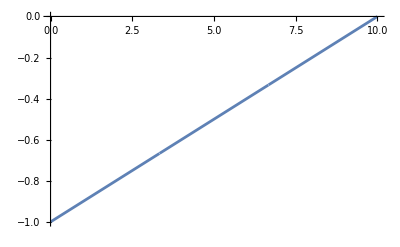

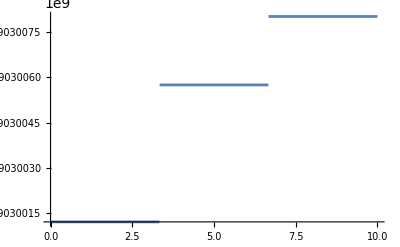

```mathematica
solq=a[[;;ndofsq]].qphi;
solp=a[[ndofsq+1;;]].pphi;
Plot[solq,{x,0,domainsize}]
Plot[solp,{x,0,domainsize}]
```

### Non linear

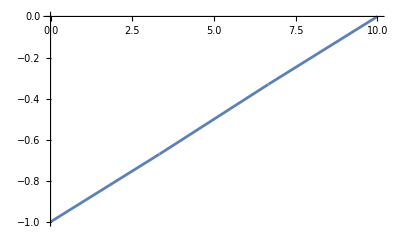

-3.6423

543074.

```mathematica
Qnodal=ConstantArray[-0.5,{ndofsq}];
Qnodal[[1]]=qin;
Qnodal[[2]]=-0.67;
Qnodal[[3]]=-0.33;
Qnodal[[4]]=0;
Qcurr=Qnodal.qphi/.cfg;
Plot[Qcurr,{x,0,domainsize}]
Integrate[Qcurr Abs[Qcurr]^(3/4),{x,0,domainsize}]
c=(2.252610888 Dw^(19/7))/(mu^(1/7)rho^(3/7));
d=c^(-7/4)/.cfg;
d/.cfg
```

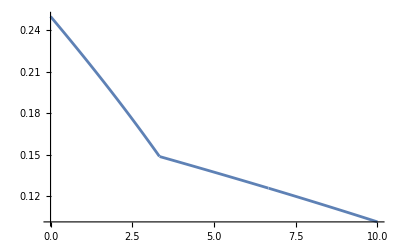

```mathematica
Plot[((Abs[Qcurr])^(3/4)+Sign[Qcurr](3 Abs[Qcurr]^(3/4))/4),{x,0,domainsize}]
```

```mathematica
maxsteps=1;
pnodal=ConstantArray[0,{ndofsp}];
Kg=ConstantArray[0,{ndofs,ndofs}];
Fg=ConstantArray[0,{ndofs}];
For[i=1,i<=maxsteps,i++,
Print["-------- Iteration ",i," ---------"];
Qcurr=Qnodal.qphi/.cfg;
pcurr=pnodal.pphi/.cfg;
dQcurr=D[Qcurr,x];
(*Kg[[1;;ndofsq,1;;ndofsq]]=Table[Integrate[d ((Abs[Qcurr])^(3/4)+(3Qcurr)/(4(Abs[Qcurr])^(1/4)))qphi[[i]]qphi[[j]],{x,0,domainsize}],{i,ndofsq},{j,ndofsq}];*)
(*Kg[[1;;ndofsq,1;;ndofsq]]=Table[Integrate[d ((Abs[Qcurr])^(3/4)+Sign[Qcurr](3 Abs[Qcurr]^(3/4))/4)qphi[[i]]qphi[[j]],{x,0,domainsize}],{i,ndofsq},{j,ndofsq}];*)
Kg[[1;;ndofsq,1;;ndofsq]]=Table[Integrate[d ((Abs[Qcurr])^(3/4)+Sign[Qcurr](3 Abs[Qcurr]^(3/4))/4)qphi[[i]]qphi[[j]],{x,0,domainsize}],{i,ndofsq},{j,ndofsq}];
Kg[[1;;ndofsq,ndofsq+1;;-1]]=-Table[Integrate[dqphi[[i]]pphi[[j]],{x,0,domainsize}],{i,ndofsq},{j,ndofsp}];
Kg[[ndofsq+1;;,1;;ndofsq]]=Transpose[Kg[[1;;ndofsq,ndofsq+1;;-1]]];
Kg[[ndofsq+1;;,ndofsq+1;;]]=Kvw Table[Integrate[pphi[[i]]pphi[[j]],{x,0,domainsize}],{i,ndofsp},{j,ndofsp}]/.cfg;
Fg[[1;;ndofsq]]= Table[Integrate[d Qcurr Abs[Qcurr]^(3/4) qphi[[i]]-dqphi[[i]]pcurr,{x,0,domainsize}],{i,ndofsq}]/.cfg;
Fg[[ndofsq+1;;]]= Table[Integrate[pphi[[i]] dQcurr+Kvw pphi[[i]]pcurr-Kvw pphi[[i]]pr,{x,0,domainsize}],{i,ndofsp}]/.cfg;

Fgn=Fg/.cfg;
Print["Kg = ",Kg//MatrixForm];
Print["Fgn = ",Fgn];
normF=Norm[Fgn];
Print["normF = ",normF];
If[normF<10^-3,Print["Converged with normF = ",normF];Break[]];

Kg[[ndofsq,;;]]=0;
Kg[[;;,ndofsq]]=0;
Kg[[ndofsq,ndofsq]]=1;
Fg[[ndofsq]]=0;

Kg[[1,;;]]=0;
Kg[[;;,1]]=0;
Kg[[1,1]]=1;
Fg[[1]]=0;

Kg=Kg/.cfg;
Fg=Fg/.cfg;

da=LinearSolve[Kg,-Fg];

Print["normda = ",Norm[da]];

Qnodal+=da[[;;ndofsq]];
pnodal+=da[[ndofsq+1;;]]
]
```

-------- Iteration 1 ---------

Kg = (141354. | 65837.3 | 0. | 0. | 1 | 0 | 0
65837.3 | 222582. | 44750.8 | 0. | -1 | 1 | 0
0. | 44750.8 | 130368. | 19107.3 | 0 | -1 | 1
0. | 0. | 19107.3 | 21836.9 | 0 | 0 | -1
1 | -1 | 0 | 0 | 4.22961×10^-11 | 0 | 0
0 | 1 | -1 | 0 | 0 | 4.22961×10^-11 | 0
0 | 0 | 1 | -1 | 0 | 0 | 4.22961×10^-11)

Fgn = {-741860.,-918941.,-292018.,-25221.6,0.329067,0.339067,0.329067}

normF = 1.21685×10^6

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.,0.,0.,0.,0.,0.,0.},{0.,222582.,44750.8,0.,-1.,1.,0.},{0.,44750.8,130368.,0.,0.,-1.,1.},{0.,0.,0.,1.,0.,0.,0.},{0.,-1.,0.,0.,4.22961×10^-11,0.,0.},{0.,1.,-1.,0.,0.,4.22961×10^-11,0.},{0.,0.,1.,0.,0.,0.,4.22961×10^-11}} may contain significant numerical errors.

normda = 1.3612×10^10

### Plotting solution

```mathematica
solq=a[[;;ndofsq]].qphi;
solp=a[[ndofsq+1;;]].pphi;
Plot[solq,{x,0,domainsize}]
Plot[solp,{x,0,domainsize}]
```

```mathematica
Clear[c,Qw,q];
D[Qw[x]Abs[(Qw[x])^(3/4)],x]
```

Abs[Qw[x]]^(3/4) Qw'[x]+(3 Qw[x] Abs'[Qw[x]] Qw'[x])/(4 Abs[Qw[x]]^(1/4))